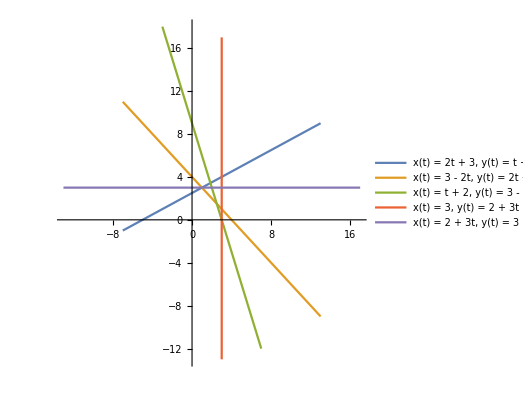

```mathematica
a=3;b=1;c=2;d=4;
ParametricPlot[{{2 t + 3,t + 4},{3-2t,2t+1},{t+2,3-3t},{3,2+3t}, {2+3t, 3}},{t,-5,5},PlotLegends->{"x(t) = 2t + 3,   y(t) = t + 4","x(t) = 3 - 2t,   y(t) = 2t + 1", "x(t) = t + 2,   y(t) = 3 - 3t", "x(t) = 3,   y(t) = 2 + 3t", "x(t) = 2 + 3t,   y(t) = 3"}]
```

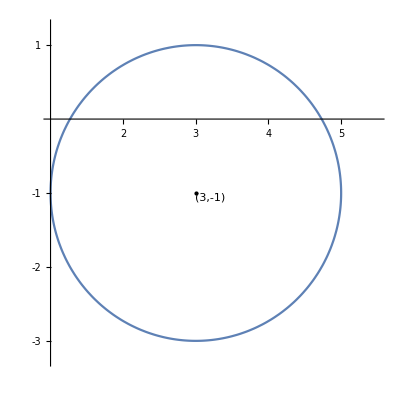

```mathematica
ParametricPlot[{2 Cos[t] + 3, 2 Sin[t] -1},{t,0,2Pi},Epilog->{PointSize[Large],Point[{3,-1}]},PlotLegends->{Placed["(3,-1)",{Scaled[{0.445,0.5}],Scaled[{0,1.35}]}]},Ticks->{{2,3,4,5},{-3,-2,-1,1}},PlotRange->{{1,5.5},{-3.25,1.25}}]
```

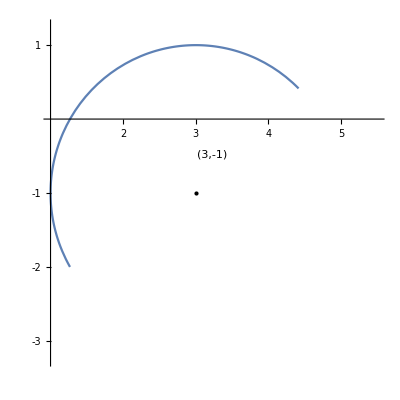

```mathematica
ParametricPlot[{2 Cos[t] + 3, 2 Sin[t] -1},{t,Pi/4,7Pi/6},Epilog->{PointSize[Large],Point[{3,-1}]},PlotLegends->{Placed["(3,-1)",{Scaled[{0.45,0.625}],Scaled[{0,2.25}]}]},Ticks->{{2,3,4,5},{-3,-2,-1,1}},PlotRange->{{1,5.5},{-3.25,1.25}}]
```

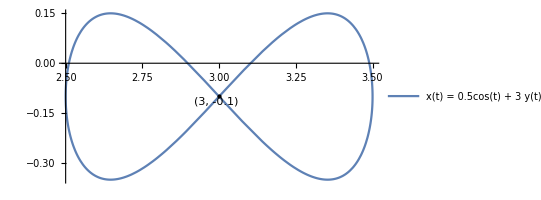

```mathematica
ParametricPlot[{1/2Cos[t] + 3, 1/4Sin[2t] -0.1},{t,0,2Pi},Epilog->{PointSize[Large],Point[{3,-0.1}]},PlotLegends->{Placed["(3, -0.1)",{Scaled[{0.42,0.5}],Scaled[{0,1.35}]}],{"x(t) = 0.5cos(t) + 3
y(t) = 0.25sin(t) - 0.1"}},Axes->Automatic]
```

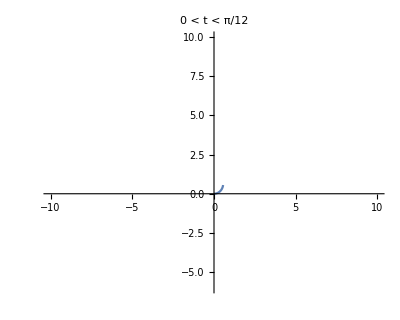
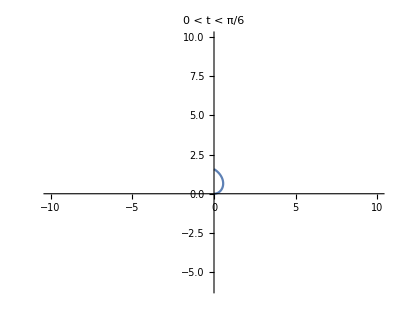
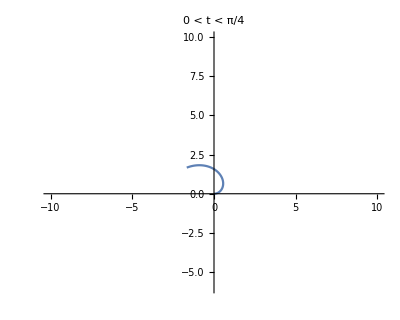
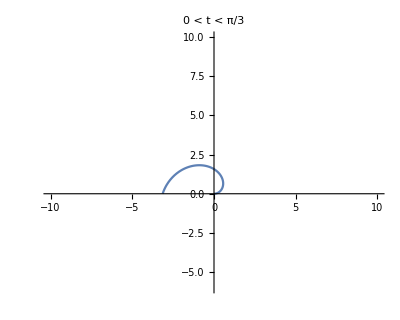
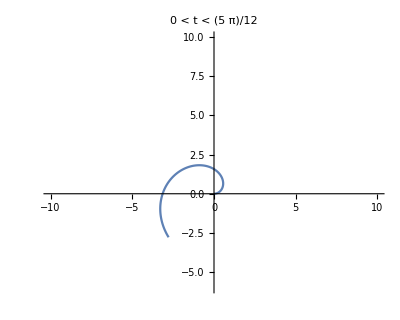
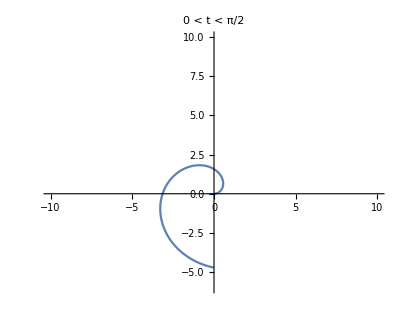
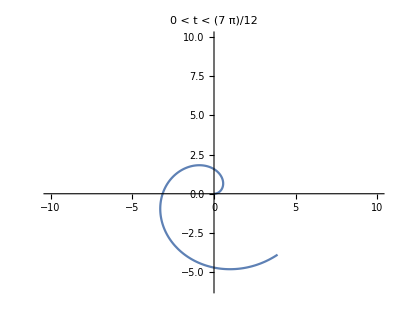
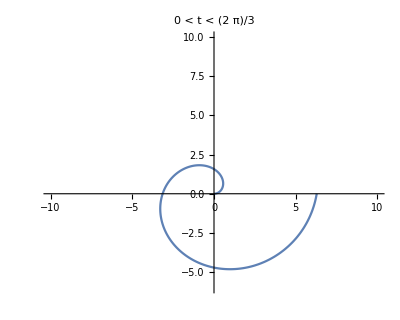

```mathematica
Table[ParametricPlot[{t Cos[t],t Sin[t]},{t,0,k Pi/4},PlotRange->{{-10,10},{-6,10}},PlotLabel -> Row[{"0 < t < ", k π/12}]],{k,1,12}]
```

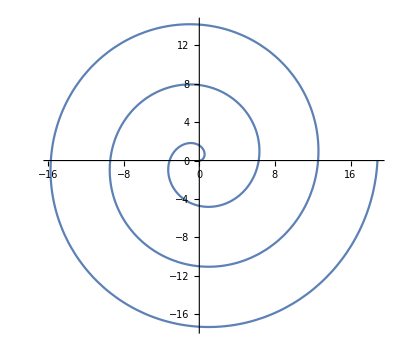

```mathematica
x0=0;
y0=0;
ParametricPlot[{t Cos[t]+x0,t Sin[t]+y0},{t,0,6Pi}(*,Epilog->Line[{{-20,y0},{25,y0}}]]*)]
```

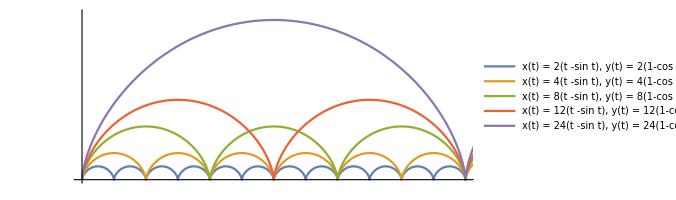

```mathematica
X[r_,t_]:=r(t-Sin[t]);
Y[r_,t_]:=r(1-Cos[t]);
ParametricPlot[{{X[2,t],Y[2,t]},{X[4,t],Y[4,t]},{X[8,t],Y[8,t]},{X[12,t],Y[12,t]},{X[24,t],Y[24,t]}},{t,0,24Pi},PlotRange->{{0,2*Pi*24+0.01},{0,50}},Ticks->None,(*Ticks->{{0,25,50,75,100,125,150},{0,4,8,16,24,48}},*)PlotLegends->{"x(t) = 2(t -sin t),   y(t) = 2(1-cos t)","x(t) = 4(t -sin t),   y(t) = 4(1-cos t)","x(t) = 8(t -sin t),    y(t) = 8(1-cos t)","x(t) = 12(t -sin t),  y(t) = 12(1-cos t)","x(t) = 24(t -sin t),  y(t) = 24(1-cos t)"}]
```

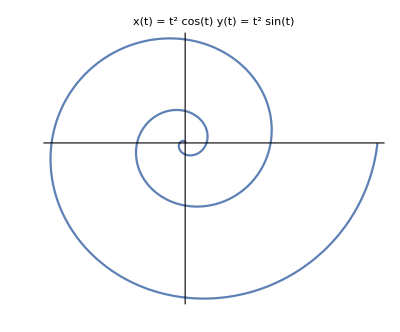
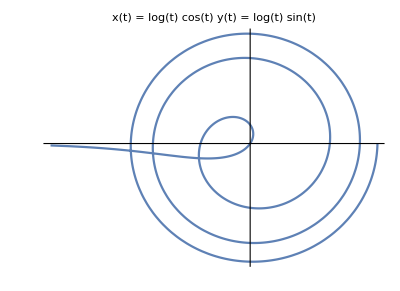
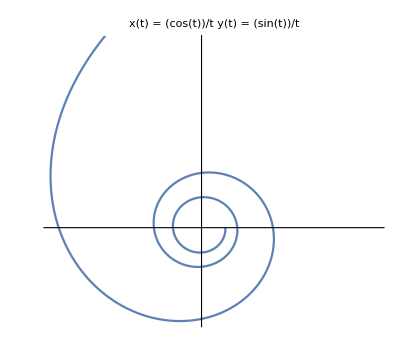
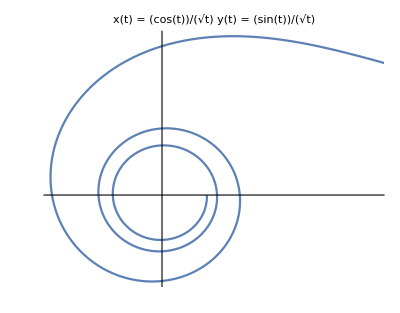
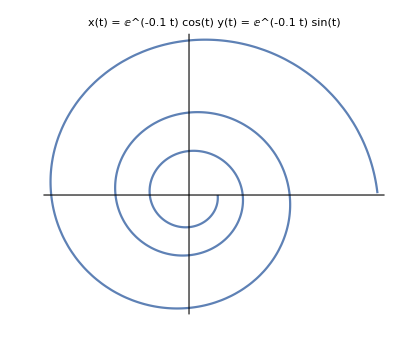

```mathematica
list={t^2,Log[t],1/t,1/Sqrt[t],Exp[-0.1 t]};
Table[ParametricPlot[{f Cos[t],f Sin[t]},{t,0.01,6Pi},PlotLabel->Row[{"x(t) = ",f Cos[t],"
y(t) = ",f Sin[t],"
"}],PlotLegends->"Expressions",Ticks->None],{f,list}]
```

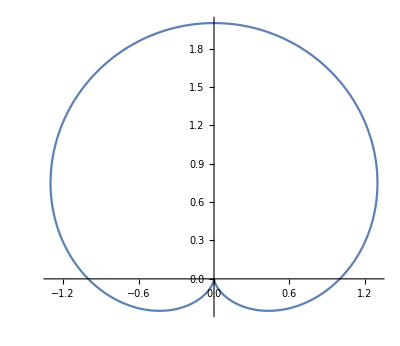

```mathematica
ParametricPlot[{(1+Sin[t])Cos[t],(1+Sin[t])Sin[t]},{t,0,2Pi}]
```

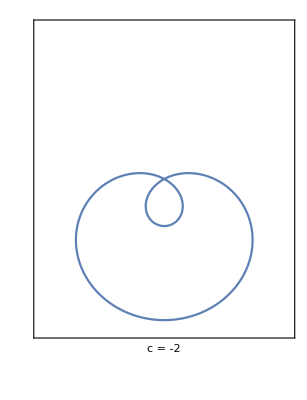
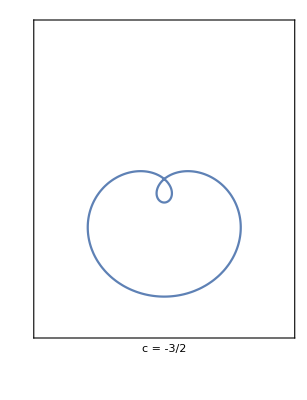
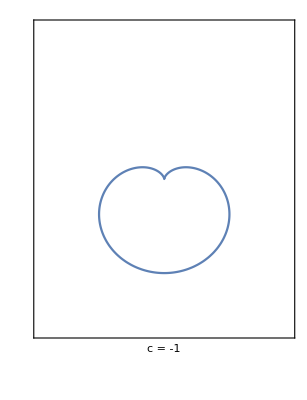
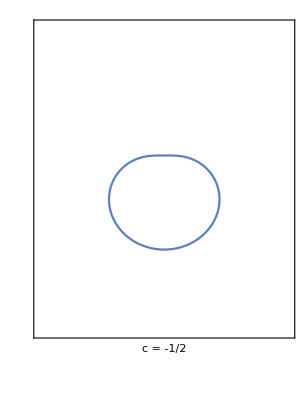
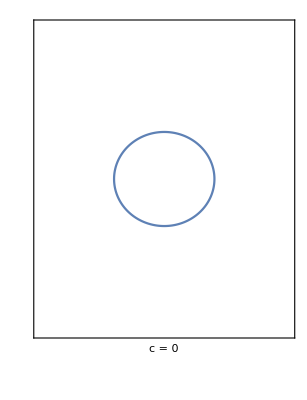
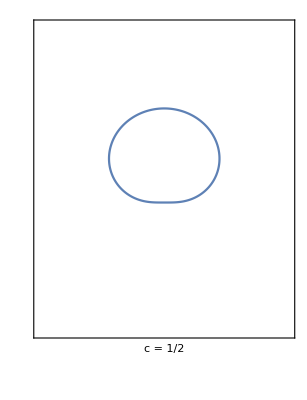
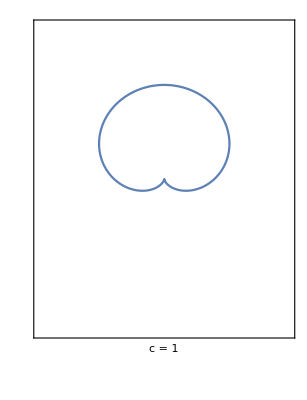
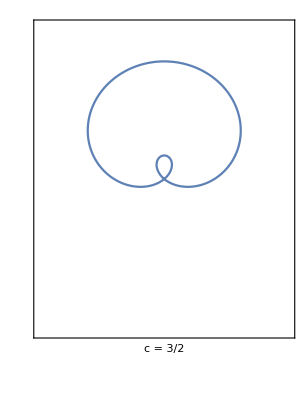

```mathematica
r=1+c Sin[t];
Table[ParametricPlot[{r Cos[t],r Sin[t]},{t,0,2Pi},PlotRange->{{-2.5,2.5},{-3.25,3.25}},Frame->True,FrameLabel->Style[Row[{"c = ",InputForm[c],""}],14],FrameTicks->None],{c,-2,2,1/2}]
```

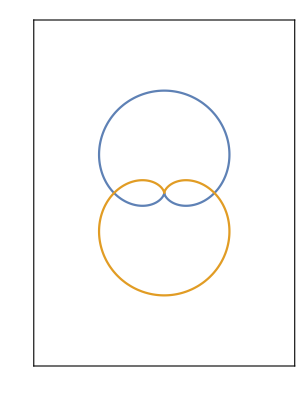

```mathematica
c=1;
r1=1+c Sin[t];
r2=1-c Sin[t];
ParametricPlot[{{r1 Cos[t],r1 Sin[t]},{r2 Cos[t],r2 Sin[t]}},{t,0,2Pi},PlotRange->{{-2.5,2.5},{-3.25,3.25}},Frame->True,FrameTicks->None]
```

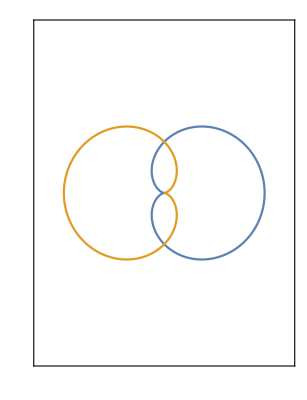

```mathematica
c=1;
r1=1+c Cos[t];
r2=1-c Cos[t];
ParametricPlot[{{r1 Cos[t],r1 Sin[t]},{r2 Cos[t],r2 Sin[t]}},{t,0,2Pi},PlotRange->{{-2.5,2.5},{-3.25,3.25}},Frame->True,FrameTicks->None]
```

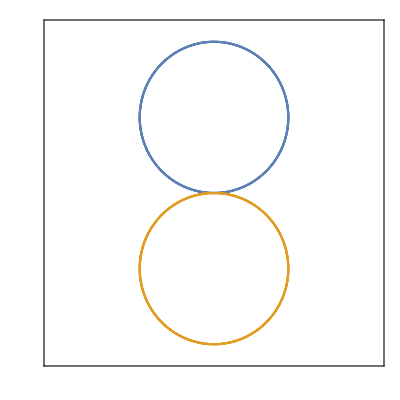

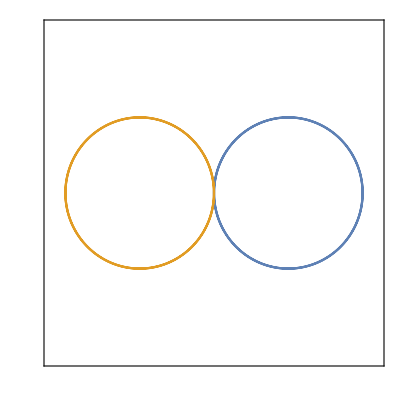

```mathematica
ClearAll[r,c,const]
c=1;
b=2;
r[t_]:=Sin[c t];
ParametricPlot[{{r[t] Cos[t],r[t] Sin[t]},{-r[t] Cos[t],-r[t] Sin[t]}},{t,0,b Pi},Ticks->None,PlotRange->{{-1.1,1.1},{-1.1,1.1}},Frame->True,FrameTicks->None]
ParametricPlot[{{r[t] Sin[t],r[t] Cos[t]},{-r[t] Sin[t],-r[t] Cos[t]}},{t,0,b Pi},Ticks->None,PlotRange->{{-1.1,1.1},{-1.1,1.1}},Frame->True,FrameTicks->None]
```

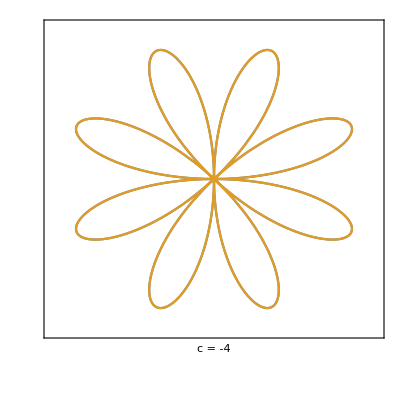
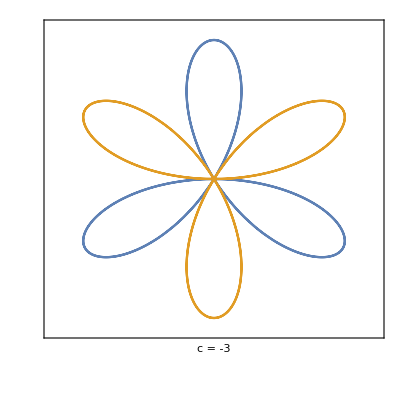
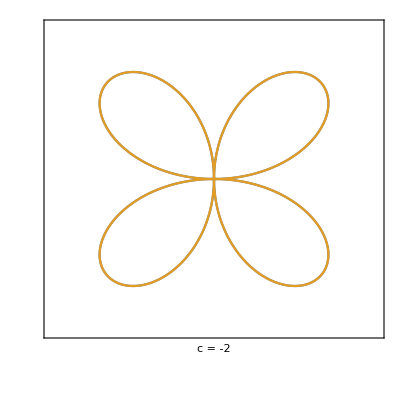
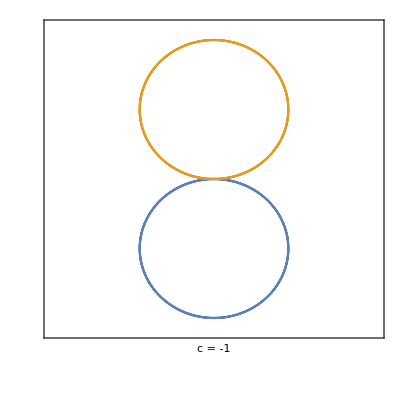
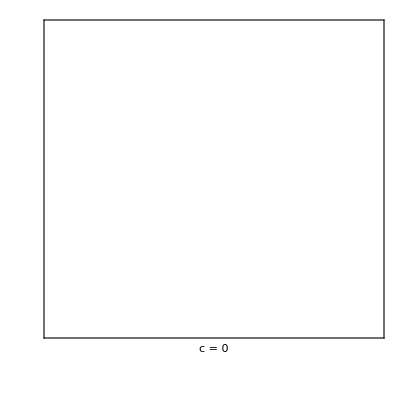
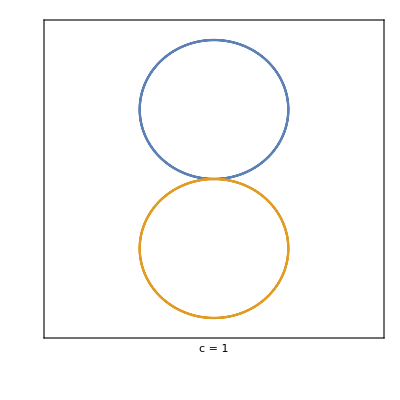
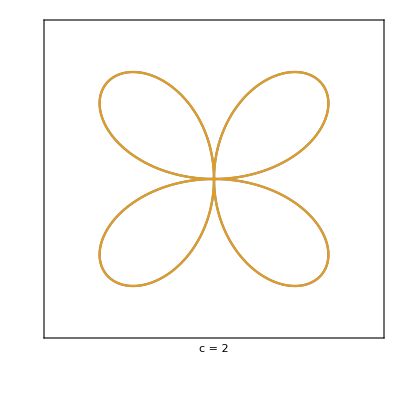
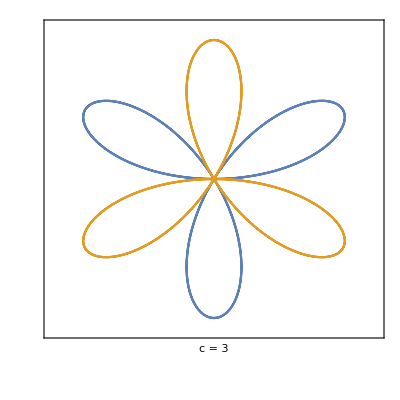

```mathematica
Table[ParametricPlot[{{r[t] Cos[t],r[t] Sin[t]},{-r[t] Cos[t],-r[t] Sin[t]}},{t,0,b Pi},Ticks->None,PlotRange->{{-1.1,1.1},{-1.1,1.1}},Frame->True,FrameTicks->None,FrameLabel->Style[Row[{"c = ",InputForm[c],""}],14]],{c,-4,4}]
```

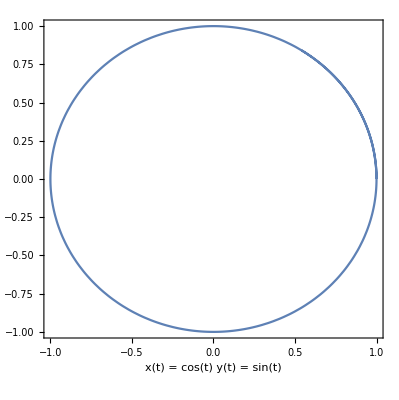
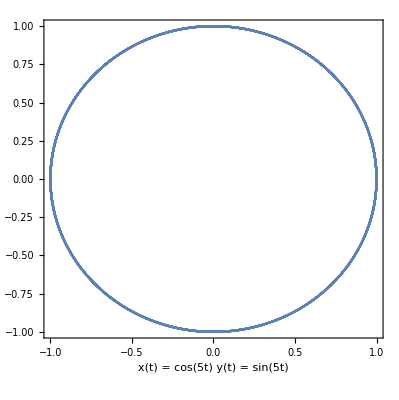
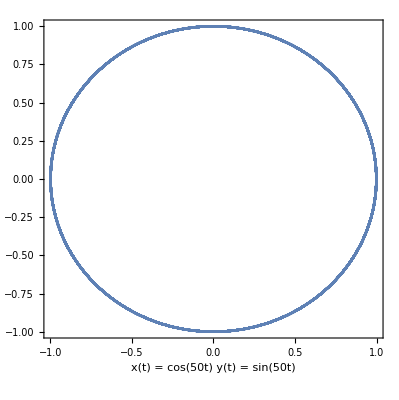

```mathematica
Table[ParametricPlot[{Cos[k t],Sin[k t]},{t,0,2Pi+1},Ticks->None,Frame->True,FrameLabel->Style[Row[{"x(t) = cos(",If[k==1,"",InputForm[k]],"t)
y(t) = sin(",If[k==1,"",InputForm[k]],"t)"}],14]],{k,{1,5,50}}]
```